## Some useful constraints

Q_u=50D f_0^(1/2)
1.0 < b/d<4/0
0.45 < d/D<0.6
0.4 < d_0/τ < 0.6, at b/d = 1.5
0.5< d_0/τ<0.7, at b/d=4.0
τ < d/2
d_0>5δ, where δ is the skin depth

A typical parameter setting as below:
N=1900/(f_0 D)
d/D=0.55
b/d>1.0

τ=1/n=(f_0 D^2)/2300 inches per turn
Z_0=98000/(f_0 D)Ω
d/D=1.55
b/d=1.5

H=b+D/2, shield height
τ<d/2

## Design tips

τ=2 d_0 will be a nice choice

Larger diameter of wire will be better, but we should consider more about the realization of helical resonator, so 3mm to 5mm will be a nice range.

Z_in=μ_0 N_a A_a/τ_a(iω+(k^2 L_c ω^2)/(iωL_c+Z_L)), A_a and τ_a is the area and winding pitch of the antenna, and it is obvious that the antenna is the key point of impedance matching for 50Ω source and it won’t affect the resonant frequency too much, but the coupling will change a little during tuning antenna so that resonant frequency will be changed a little as well.

V=κ √PQ, κ=(L/C)^(1/4) or we can use an approximate formula κ=√(4/π^2 √(μ_0/ϵ_0)ln(D/d)), the geometry factor is usually in the range (10,20).

The resonant frequency strongly depends on the winding pitch and coil diameter, so the coil should be manufactured with precision, and a rigid mount is required to make the resonant frequency stable.

## Tips for constructing helical resonator

In order to minimise the resistance of the solder joint, any solder joints should be made with a clean oxide free surface before soldering, with both parts of the joint reaching a sufficient temperature to ensure good solder flow between them.

Furthermore, we can estimate the resistance of the solder joint with a known resistance R_s measured at a known frequency ω_s, then the resistance should be
R_0=R_s √(ω_0/ω_s)

## A helpful design procedure from coil32.net

-Graphics-
-Graphics-

Initial data for calculation:
Working frequency - f_0
Bandwidth on level -3 dB - ΔF
Admissible loss in the passband - α
Input and output impedance - R_i, R_u
Suppose we have the following data: f0 = 100MHz; ΔF = 1МГц; Ri = Ru = 50 Ohm; α = 1 dB

We define the unloaded Q of the resonator Q_u
Q_u = (f_0/ΔF)Q_0
Q_0 = 1.414/(10^(α/20) - 1)

Q_0 = 1.414/(101/20 - 1) = 11.59;
Q_u = (100/1)9.35 = 1159;

The formulas [3.1] and [3.6] define the size of the helix:
d = Q_u / (35.9 √f_0) = 935 / (35.9·√100) = 1159 / 359 = 3.2 cm; 
b = 1.5d = 1.5·3.2 = 4.8 cm;

The formulas [3.3], [3.4], [3.5] define the number of turns, winding pitch and diameter of the wire:
N = 2674 / (100·3.2) = 8.3 turns;
τ = 4.8 / 8.3 = 5.8 mm;
d0 = 5.8 / 2 = 2.9 mm;

The formulas [2.1], [2.3] define the size of the shield:
S = 3.2 / 0.66 = 4.9 cm;
H = 4.9·1.6 = 7.8 cm;

We define where is the tap from the grounded end of the coil. To do this we define the twice-loaded (with both input and output) quality factor of the filter Q_d:
Q_d = 0.5q1f0/ΔF;   
q_1 = 1.414 for 2-element filter	[4.2] 

Q_d = 0.5·1.414·100/1 = 70.70;

Next, we use the following expressions:

R_b/Z_0 = π/4(1/Q_d - 1/Q_u)	[4.3]
sin(θ) = √((0.5 R_b/Z_0) (R_tap Z_0))	[4.4]

R_tap - input / output filter resistance (R_i or R_u) in this example are equal
θ - the electrical length from the grounded end to the tap

tap = Nθ°/90°	[4.5]

tap - the number of turns from the cold end to the tap

R_b/Z_0 = π/4(1/70.70 - 1/1159) = 0.01;

  According to the formula[3.7] define the Z0:
 Z_0= 136190/(100·3.2) = 421.9;
sin(θ) = √((0.5·0.01)·(50/421.9)) = 0.0243;
θ = 1.39°;
tap = 8.3·1.39/90 = 0.13 turns from the cold end of the helix.
Since the input and output impedances are the same, the both taps of resonators are also the same, otherwise the calculation should be conducted separately for each tap.

Next we will get the size of the coupling window. This is the dimension “h” on the diagram,  the distance from the coupling window to the hot end of the helix. For 2-elements filter:

(h/d)1.91 = 10 (ΔF/f0)	[4.6] 

(h/d)1.91 = 10 (1/100) = 0.1;
h/d = 0.3;
h = 0.3·3.2 = 0.97 cm;
The calculation allows to determine the minimum size of the helical tank. Naturally, starting from “3” step we can increase them. For calculation of two-element filter by Zverev’s method you can use the online calculator . Number of helical resonators in the filter defines the squareness ratio frequency response of the filter. By increasing the number of resonators calculation becomes much more complicated.

## Function definitions(Siverns and Ke Deng)

```mathematica
ClearAll[CoilCapacitanceEfficient,CoilHeight,CoilInductanceEfficient,CapacitanceCoil,CapacitanceShield,ResistanceCoil,ResistanceShield,InductanceCoil,LengthCoil,NumberTurns,SkinDepth,EffectiveCapacitance,Quality1,Quality2,ShieldCapacitanceEfficient];CoilCapacitanceEfficient[b_,dc_]:=(11.26 b/dc+8+27/(√(b/dc)))*10^-12;

CapacitanceCoil[b_,dc_] :=CoilCapacitanceEfficient[b,dc]*dc;

ShieldCapacitanceEfficient[dc_,ds_] :=39.37*0.75/Log10[ds/dc]*10^-12;

CapacitanceShield[b_,dc_,ds_] :=b *ShieldCapacitanceEfficient[dc,ds];

CoilInductanceEfficient[dc_,ds_,τ_]:= (39.37*(0.025 *dc^2(1-(dc/ds)^2))/τ^2)*10^-6;

InductanceCoil[b_,dc_,ds_,τ_] := b*CoilInductanceEfficient[dc,ds,τ];


LengthCoil[b_,dc_,τ_]:=b/τ √(τ^2+(π dc)^2);

NumberTurns[b_,dc_,τ_,ds_]:=(LengthCoil[b,dc,τ]*b)/(4π (ds-dc)^2);

LengthShield[b_,dc_,τ_,ds_]:=√((π *NumberTurns[b,dc,τ,ds]*ds)^2+b^2);

SkinDepth[ρ_,f_]:=√(ρ/(f*4 π^2*10^-7));
ResistanceCoil[b_,dc_,τ_,d0_,ρ_,f_]:=ρ*LengthCoil[b,dc,τ]/(d0*π*SkinDepth[ρ,f]);


ResistanceShield[b_,dc_,τ_,ds_,d0_,ρ_,f_]:=(ρ*NumberTurns[b,dc,τ,ds]*LengthShield[b,dc,τ,ds])/(b*SkinDepth[ρ,f]);


EffectiveCapacitance[b_,dc_,τ_,ds_]:=Module[{n,Ccu,Csu,Ceff},
n=Ceiling[b/τ];
Ccu = CapacitanceCoil[b,dc]*(n-1);
Csu = CapacitanceShield[b,dc,ds]/(n-1);
Ceff = Nest[(1/(1/#+1/Ccu)+Csu)&,Ccu+Csu,n-1]];

CoilHeight[dc_,ds_,τ_,f_,Ct_,Cw_]:=Module[
{Kcd,Kcb,Kcs,KLc,b},
Kcd=35*dc*10^-12;
Kcb=11.26 10^-12;
Kcs=ShieldCapacitanceEfficient[dc,ds];
KLc=CoilInductanceEfficient[dc,ds,τ];
b=((Ct+Cw+Kcd)/(Kcs+Kcb))*(√((Kcs+Kcb)/((Ct+Cw+Kcd)^2*KLc*(2π f)^2)+1/4)-1/2)
]

Quality1[dc_,ds_,d0_,τ_,Ct_,Rt_,Cw_,Rj_,f_,ρ_]:=Module[{b,Rc,Rs,Cs,Lc,Cc,ω,Resr,α,Resr0,Q0,Q},
(*ω = f*2π;*)
b=CoilHeight[dc,ds,τ,f,Ct,Cw];
Rc = ResistanceCoil[b,dc,τ,d0,ρ,f];
Rs = ResistanceShield[b,dc,τ,ds,d0,ρ,f];
Lc = InductanceCoil[b,dc,ds,τ];
Cc = CapacitanceCoil[b,dc];
Cs = CapacitanceShield[b,dc,ds];
(*Resr= (Rc*1/(ω*Cc)^2)/(Rc^2+(1/(ω*Cc)+ω*Lc)^2)+(Rt*(1/(ω*(Cs+Cw)))^2)/(Rt^2+(1/(ω*(Cs+Cw))+1/(ω*Ct))^2)+Rs+Rj;*)
Resr0=Rc+Rs+Rj √(f √((Cs+Cc+Ct+Cw)/(Cs+Cc))×10^-7);
α=Ct/(Cs+Cw);
Resr= Rc+Rs+Rt*(α/(α+1))^2+Rj √(f×10^-7);
(*Resr= Rc+Rs+Rt*(α/(α+1))^2+Rj;*)
{Q0=1/Resr √(Lc/(Cc+Cs)),Q=1/Resr √(Lc/(Cc+Cs+Ct+Cw))}
];
QualityOld[dc_,b_,ds_,d0_,τ_,Ct_,Rt_,Cw_,Rj_,ρ_]:=Module[{Rc0,Rs0,Rc,Rs,Cs,Lc,Cc,ω,Resr,α,Resr0,f0,f,Q0,Q},
Lc = InductanceCoil[b,dc,ds,τ];
Cc = CapacitanceCoil[b,dc];
Cs = CapacitanceShield[b,dc,ds];
f0=1/(2π √(Lc(Cs+Cc)));
f=1/(2π √(Lc(Cs+Cc+Ct+Cw)));
Rc0 = ResistanceCoil[b,dc,τ,d0,ρ,f0];
Rs0 = ResistanceShield[b,dc,τ,ds,d0,ρ,f0];
Rc = ResistanceCoil[b,dc,τ,d0,ρ,f];
Rs = ResistanceShield[b,dc,τ,ds,d0,ρ,f];

(*Resr= (Rc*1/(ω*Cc)^2)/(Rc^2+(1/(ω*Cc)+ω*Lc)^2)+(Rt*(1/(ω*(Cs+Cw)))^2)/(Rt^2+(1/(ω*(Cs+Cw))+1/(ω*Ct))^2)+Rs+Rj;*)
Resr0=Rc+Rs+Rj √(f0×10^-7);
α=Ct/(Cs+Cw);
Resr= Rc+Rs+Rt*(α/(α+1))^2+Rj √(f×10^-7);
(*Resr= Rc+Rs+Rt*(α/(α+1))^2+Rj;*)
{Q0=1/Resr √(Lc/(Cc+Cs)),Q=1/Resr √(Lc/(Cc+Cs+Ct+Cw))}
];
(*Modified model: it can be used to verify if the design good enough or not*)
Frequency[dc_,b_,ds_,τ_,Ct_,Cw_]:=Module[
{Lc,f1,f2,f0,f,Ce,Cc,Cs},
Lc = InductanceCoil[b,dc,ds,τ];
Ce=EffectiveCapacitance[b,dc,τ,ds];
Cc=CapacitanceCoil[b,dc];
Cs=CapacitanceShield[b,dc,ds];
{{f0=1/(2π √((Cs+Cc)*Lc)) ,f1=1/(2π √(Ce*Lc))},{f2=1/(2π √((Cc+Cs+Ct+Cw)*Lc)) ,f=1/(2π √((Ce+Cw+Ct)*Lc))}}
]
(*This quality function is not a good choice, since the frequency dependence is not the same as Siverns*)
Quality2[dc_,ds_,d0_,τ_,Ct_,Rt_,Cw_,Rj_,f_,ρ_]:=Module[{δ,b,Rc,Rs,Cs,Lc,Cc,Resr,Q0,Q,Ceff,Resr0,Rs0,Rc0},
δ = SkinDepth[ρ,f];
b =CoilHeight[dc,ds,τ,f,Ct,Cw];
Lc = InductanceCoil[b,dc,ds,τ];
Ceff = EffectiveCapacitance[b,dc,τ,ds];
Rc0 = ResistanceCoil[b,dc,τ,d0,ρ,1/(2π √(Lc×Ceff))]; 
Rs0 = ResistanceShield[b,dc,τ,ds,d0,ρ,1/(2π √(Lc×Ceff))];
Rc = ResistanceCoil[b,dc,τ,d0,ρ,1/(2π √(Lc(Ceff+Ct+Cw)))]; 
Rs = ResistanceShield[b,dc,τ,ds,d0,ρ,1/(2π √(Lc(Ceff+Ct+Cw)))];

Resr0=Rc0+Rs0+Rj √(1/(2π √(Lc×Ceff))×10^-7);
Resr= Rc+Rs+Rt*(Ct/(Ct+Ceff))^2+Rj √(1/(2π √(Lc(Ceff+Ct+Cw)))×10^-7);

{Q0 = 1/Resr0 √(Lc/Ceff) ,Q = 1/Resr √(Lc/(Ceff+Ct+Cw))}];

 QualityNew[dc_,b_,ds_,d0_,τ_,Ct_,Rt_,Cw_,Rj_,ρ_]:=Module[{δ,Rc,Rs,Cs,Rc0,Rs0,Lc,Cc,Resr0,Resr,Q0,Q,Ceff,f0,f},
f0=1/(2π √(Lc×Ceff));
f=1/(2π √(Lc(Ceff+Ct+Cw)));
Lc = InductanceCoil[b,dc,ds,τ];
Ceff = EffectiveCapacitance[b,dc,τ,ds];
Rc0 = ResistanceCoil[b,dc,τ,d0,ρ,f0]; 
Rs0 = ResistanceShield[b,dc,τ,ds,d0,ρ,f0];
Rc = ResistanceCoil[b,dc,τ,d0,ρ,f]; 
Rs = ResistanceShield[b,dc,τ,ds,d0,ρ,f];

Resr0=Rc0+Rs0+Rj √(f0×10^-7);
Resr= Rc+Rs+Rt*(Ct/(Ct+Ceff))^2+Rj √(f×10^-7);

{Q0 = 1/Resr0 √(Lc/Ceff),Q = 1/Resr √(Lc/(Ceff+Ct+Cw))}];
(*QualityAll[dc_,ds_,b_,d0_,τ_,Ct_,Rt_,Cw_,Rj_,f_,ρ_]:=Module[
{δ,Rc,Rs,Cs,h,Lc,Cc,Resr,Q0,Q,Ceff},
δ = SkinDepth[ρ,f];
h =CoilHeight[dc,ds,τ,f,Ct,Cw];
Rc = ResistanceCoil[b,dc,τ,d0,ρ,f]; 
Rs = ResistanceShield[b,dc,τ,ds,d0,ρ,f];
Lc = InductanceCoil[b,dc,ds,τ];
Ceff = EffectiveCapacitance[b,dc,τ,ds];
Resr= Rc+Rs+Rt*(Ct/(Ct+Ceff))^2+Rj √(f×10^-7);
{{1/Resr √(Lc/Ceff)}}
];*)
```

## A typical external parameters

C_t=8pF, C_w=0.1pF, R_t=2Ω, R_j=0.5Ω, The trap capacitance is measured at 300kHz and 1MHz with 8pF and 18pF respectively. Furthermore, the inductance of the coil is around 1.8μH.

## Initial setup(SI units)

```mathematica
Subscript[d, 0] = 0.003;
τ = 0.01;
Subscript[f, 0] = 50 10^6;
Subscript[C, w] = 0.3 10^-12; 
Subscript[C, t] = 5 10^-12;
Subscript[R, t] = 1;
ρ = 1.68 10^-8;
Subscript[R, j] = 0.2;
```

## ContourPlot

```mathematica
ClearAll[QualityN1,QualityN2,QualityN3,QualityN4];(*QualityN1[dc_,ds_]/;CoilHeight[35*dc*10^-12,11.26 10^-12,ShieldCapacitanceEfficient[dc,ds],CoilInductanceEfficient[dc,ds,τ],Subscript[C, t],Subscript[C, w],Subscript[f, 0]]<dc||CoilHeight[35*dc*10^-12,11.26 10^-12,ShieldCapacitanceEfficient[dc,ds],CoilInductanceEfficient[dc,ds,τ],Subscript[C, t],Subscript[C, w],Subscript[f, 0]]>4dc:=0//N;*)
QualityN1[dc_,ds_]:=Quality1[dc,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],Subscript[f, 0],ρ]//N;
QualityN2[dc_,ds_]:=Quality2[dc,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],Subscript[f, 0],ρ]//N;
QualityN3[dc_,b_,ds_]:=QualityOld[dc,b,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],ρ]//N;
QualityN4[dc_,b_,ds_]:=QualityNew[dc,b,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],ρ]//N;
```

### Use contour plot to find a good data in geometry

However, this method would sometimes cause a solution out of the limitation range, and the shield diameter should be chosen in advance in practice, so it can be a ancilla method.

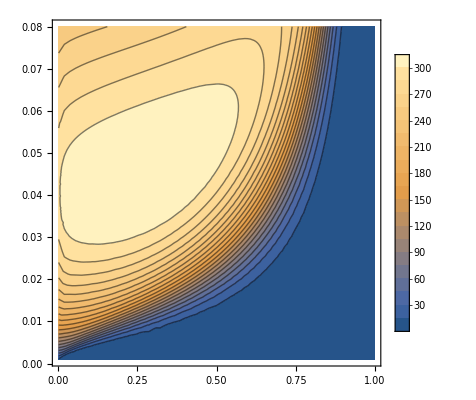

```mathematica
ContourPlot[QualityN1[y,y/k]⟦2⟧,{k,0.001,0.999},{y,0.001,0.08},PlotLegends->Automatic,ContourLabels->Automatic,Contours->20,ContourStyle->Black,MeshStyle->{Red, Blue}]
```

```mathematica
opt =NMaximize[{QualityN1[x,x/y]⟦2⟧,CoilHeight[x,x/y,τ,Subscript[f, 0],Subscript[C, t],Subscript[C, w]]/x>1&&CoilHeight[x,x/y,τ,Subscript[f, 0],Subscript[C, t],Subscript[C, w]]/x<4&&x>0.02&&x<0.06&&y>0.45&&y<0.6},{x,y},Method->"SimulatedAnnealing"]
```

{311.521,{x→0.048075,y→0.45}}

### Geometry parameters

```mathematica
Dc=x/.opt⟦2⟧
b=CoilHeight[x,x/y,τ,Subscript[f, 0],Subscript[C, t],Subscript[C, w]]/.opt⟦2⟧
n=b/τ
B=b+x/(2 y)/.opt⟦2⟧
Ds=x/y/.opt⟦2⟧
Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]]
(*unloaded frequency with two models and loaded frequency with two models*)
QualityN3[Dc,b,Ds](*unloaded quality and loaded quality factor*)
```

0.048075

0.048075

4.8075

0.101492

0.106833

{{6.78042×10^7,8.7555×10^7},{5.×10^7,5.65293×10^7}}

{422.449,311.521}

### Modified quality factor

```mathematica
QualityN4[Dc,b,Ds]
```

{642.133,316.273}

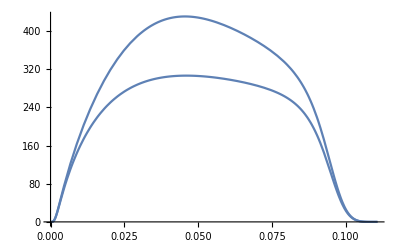

```mathematica
Plot[QualityN1[x,Ds],{x,0,Ds}]
```

### Impedance parameters

```mathematica
ResistanceCoil[b,Dc,τ,Subscript[d, 0],ρ,Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]]](*unloaded resistance(Siverns-K.Deng), loaded resistance(Siverns-K.Deng)*)
ResistanceShield[b,Dc,τ,Ds,Subscript[d, 0],ρ,Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]]]
Subscript[R, j] √(Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]] 10^-7)(*Solder junction resistance*)
CapacitanceCoil[b,Dc]
CapacitanceShield[b,Dc,Ds]
InductanceCoil[b,Dc,Ds,τ]
```

{{0.0998602,0.114982},{0.0774148,0.0807607}}

{{0.00800757,0.00922015},{0.00620773,0.00647602}}

{{0.554293,0.638228},{0.429706,0.448277}}

1.8607×10^-12

3.96286×10^-12

7.37251×10^-7

## Optimization with a given shield diameter(Old)

### Initial setup(SI units)

```mathematica
Subscript[d, 0] = 0.002;
τ = 0.006;
Subscript[f, 0] = 50 10^6;
Subscript[C, w] = 0.5 10^-12; 
Subscript[C, t] = 5 10^-12;
Subscript[R, t] = 1;
ρ = 1.68 10^-8;
Subscript[R, j] = 0.1;
ClearAll[QualityN1,QualityN2,QualityN3,QualityN4];
QualityN1[dc_,ds_]:=Quality1[dc,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],Subscript[f, 0],ρ]//N;
QualityN2[dc_,ds_]:=Quality2[dc,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],Subscript[f, 0],ρ]//N;
QualityN3[dc_,b_,ds_]:=QualityOld[dc,b,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],ρ]//N;
QualityN4[dc_,b_,ds_]:=QualityNew[dc,b,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],ρ]//N;
```

```mathematica
Subscript[D, s]=0.075;
Ds=Subscript[D, s];
```

### Optimization with combined contour plot

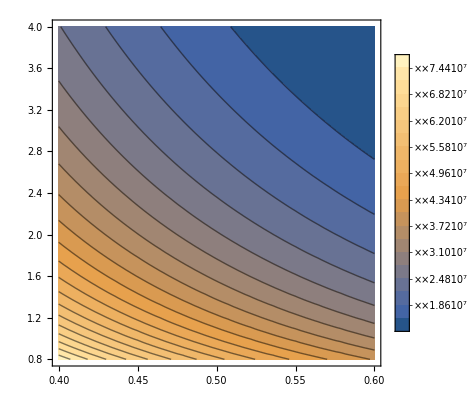

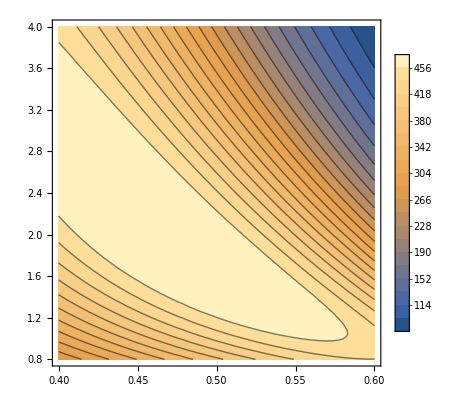

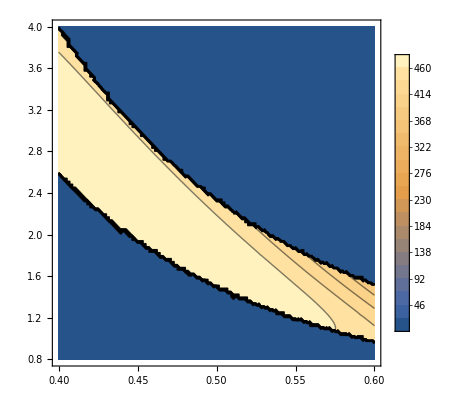

```mathematica
fre = 25 10^6;ContourPlot[Frequency[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]⟦2,1⟧,{r1,0.4,0.6},{r2,0.8,4},ContourStyle->Black,PlotLegends->Automatic,Contours->20]
ContourPlot[QualityN3[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s]]⟦2⟧,{r1,0.4,0.6},{r2,0.8,4},Contours->20,PlotRange->All,PlotLegends->Automatic]
ContourPlot[If[Frequency[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]⟦2,1⟧≥ fre&&Frequency[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]⟦2,1⟧≤ 35 10^6,QualityN3[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s]]⟦2⟧,0],{r1,0.4,0.6},{r2,0.8,4},Contours->20,PlotRange->All,PlotLegends->Automatic]
```

### Choose a set of parameters best for our experiment(fix the frequency and then find the optimal quality factor)

```mathematica
sol={r1-> 0.518,r2-> 1.55}
```

{r1→0.518,r2→1.55}

### Geometry parameters

```mathematica
Dc=Subscript[D, s]*r1/.sol
b=r2*Dc/.sol
B=b+Subscript[D, s]/2
n=b/τ
QualityN3[Dc,b,Subscript[D, s]]
Frequency[Dc,b,Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]
```

0.03885

0.0602175

0.0977175

10.0363

{624.183,481.173}

{{4.1587×10^7,6.03757×10^7},{3.20588×10^7,3.86592×10^7}}

### Impedance parameters

```mathematica
ResistanceCoil[b,Dc,τ,Subscript[d, 0],ρ,Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]]](*unloaded resistance(Siverns-K.Deng), loaded resistance(Siverns-K.Deng)*)
ResistanceShield[b,Dc,τ,Ds,Subscript[d, 0],ρ,Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]]]
Subscript[R, j] √(Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]] 10^-7)(*Solder junction resistance*)
CapacitanceCoil[b,Dc]
CapacitanceShield[b,Dc,Ds]
InductanceCoil[b,Dc,Ds,τ]
```

{{0.324168,0.390591},{0.28462,0.312549}}

{{0.131634,0.158606},{0.115575,0.126916}}

{{0.203929,0.245715},{0.17905,0.196619}}

1.83139×10^-12

6.22421×10^-12

1.81814×10^-6

## Optimization with a given shield diameter(New)

### Initial setup(SI units)

```mathematica
Subscript[d, 0] = 0.004;
τ = 0.008;
Subscript[f, 0] = 24 10^6;
Subscript[C, w] = 0.3 10^-12;
Subscript[C, t] = 8 10^-12;
Subscript[R, t] = 0.5;
ρ = 1.68 10^-8;
Subscript[R, j] = 0.2;
ClearAll[QualityN1,QualityN2,QualityN3];
QualityN1[dc_,ds_]:=Quality1[dc,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],Subscript[f, 0],ρ]//N;
QualityN2[dc_,ds_]:=Quality2[dc,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],Subscript[f, 0],ρ]//N;
QualityN3[dc_,b_,ds_]:=QualityOld[dc,b,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],ρ]//N;
QualityN4[dc_,b_,ds_]:=QualityNew[dc,b,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],ρ]//N;
```

```mathematica
Subscript[D, s]=0.103;
```

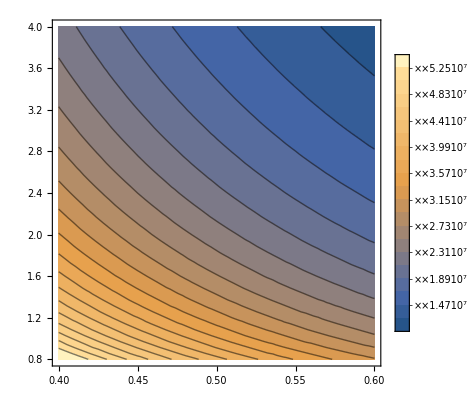

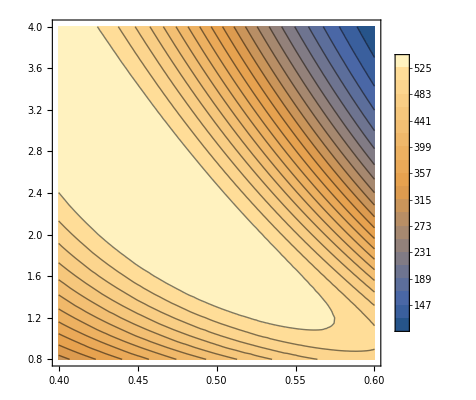

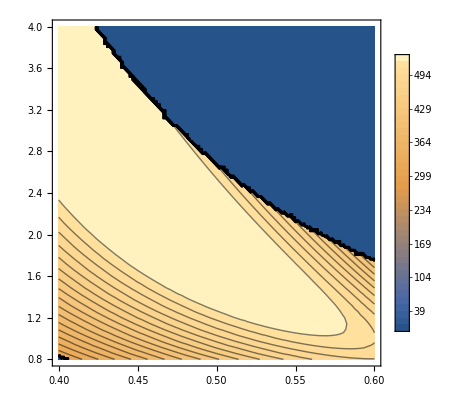

```mathematica
fre=20 10^6;
ContourPlot[Frequency[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]⟦2,2⟧,{r1,0.4,0.6},{r2,0.8,4},ContourStyle->Black,PlotLegends->Automatic,Contours->20]
ContourPlot[QualityN4[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s]]⟦2⟧,{r1,0.4,0.6},{r2,0.8,4},Contours->20,PlotRange->All,PlotLegends->Automatic]
ContourPlot[If[Frequency[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]⟦2,2⟧≥ fre&&Frequency[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]⟦2,2⟧≤ 55 10^6,QualityN4[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s]]⟦2⟧,0],{r1,0.4,0.6},{r2,0.8,4},Contours->40,PlotRange->All,PlotLegends->Automatic](*regime over 40MHz*)
```

### Choose a set of parameters best for our experiment(fix the frequency and then find the optimal quality factor)

```mathematica
sol={r1-> 0.5,r2-> 2.0}
```

{r1→0.5,r2→2.}

### Geometry parameters

```mathematica
Ds=Subscript[D, s]
Dc=Subscript[D, s]*r1/.sol
b=r2*Dc/.sol
B=b+Subscript[D, s]/2
n=b/τ
QualityN4[Dc,b,Subscript[D, s]]
Frequency[Dc,b,Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]
```

0.103

0.0515

0.103

0.1545

12.875

{870.418,555.303}

{{2.52009×10^7,3.7691×10^7},{1.95851×10^7,2.39981×10^7}}

### Impedance parameters

```mathematica
ResistanceCoil[b,Dc,τ,Subscript[d, 0],ρ,Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]]](*unloaded resistance(Siverns-K.Deng), loaded resistance(Siverns-K.Deng)*)
ResistanceShield[b,Dc,τ,Ds,Subscript[d, 0],ρ,Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]]]
Subscript[R, j] √(Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]] 10^-7)(*Solder junction resistance*)
CapacitanceCoil[b,Dc]
CapacitanceShield[b,Dc,Ds]
InductanceCoil[b,Dc,Ds,τ]
EffectiveCapacitance[Dc,b,τ,Subscript[D, s]]
```

{{0.214569,0.262409},{0.189157,0.209386}}

{{0.168934,0.206599},{0.148926,0.164853}}

{{0.317496,0.388284},{0.279893,0.309826}}

2.55501×10^-12

1.01031×10^-11

3.15093×10^-6

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

## Optimization for useless copper tube

The original design is 
- D=103mm
- h=185mm

### Initial settings

```mathematica
Subscript[d, 0] = 0.004;
τ = 0.009;
Subscript[f, 0] = 20 10^6;
Subscript[C, w] = 0.3 10^-12;
Subscript[C, t] = 15 10^-12;
Subscript[R, t] = 1;
ρ = 1.68 10^-8;
Subscript[R, j] = 0.2;
ClearAll[QualityN1,QualityN2,QualityN3,QualityN4];
QualityN1[dc_,ds_]:=Quality1[dc,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],Subscript[f, 0],ρ]//N;
QualityN2[dc_,ds_]:=Quality2[dc,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],Subscript[f, 0],ρ]//N;
QualityN3[dc_,b_,ds_]:=QualityOld[dc,b,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],ρ]//N;
QualityN4[dc_,b_,ds_]:=QualityNew[dc,b,ds,Subscript[d, 0],τ,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],ρ]//N;
```

```mathematica
Subscript[D, s]=0.103;
h=0.148;
b=h-Subscript[D, s]/2
```

0.0965

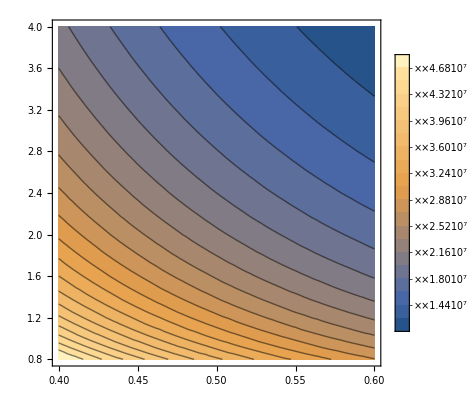

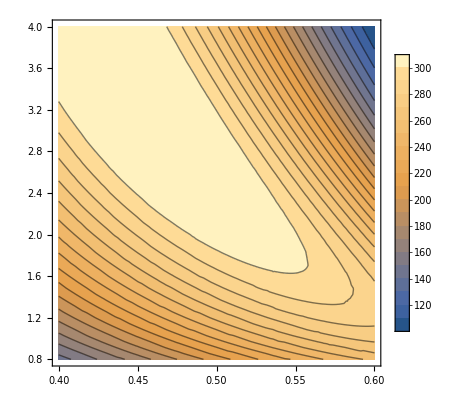

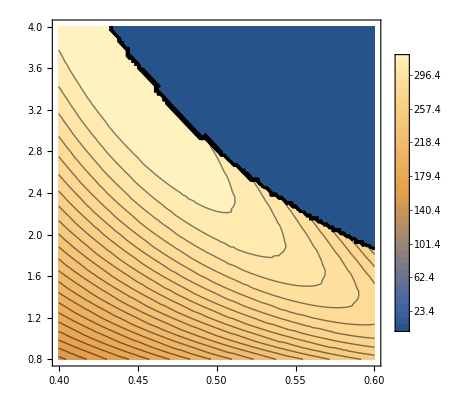

```mathematica
fre=18 10^6;
ContourPlot[Frequency[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]⟦2,2⟧,{r1,0.4,0.6},{r2,0.8,4},ContourStyle->Black,PlotLegends->Automatic,Contours->20]
ContourPlot[QualityN4[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s]]⟦2⟧,{r1,0.4,0.6},{r2,0.8,4},Contours->20,PlotRange->All,PlotLegends->Automatic]
ContourPlot[
If[Frequency[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]⟦2,2⟧≥ fre&&Frequency[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]⟦2,2⟧≤ 55 10^6,QualityN4[r1*Subscript[D, s],r1*r2*Subscript[D, s],Subscript[D, s]]⟦2⟧,0],{r1,0.4,0.6},{r2,0.8,4},Contours->40,PlotRange->All,PlotLegends->Automatic]
```

### Choose a set of parameters best for our experiment(fix the frequency and then find the optimal quality factor)

```mathematica
sol={r1-> 0.6,r2-> 2.1}
```

{r1→0.6,r2→2.1}

### Geometry parameters

```mathematica
Ds=Subscript[D, s]
Dc=Subscript[D, s]*r1/.sol
b=r2*Dc/.sol
B=b+Subscript[D, s]/2
n=b/τ
QualityN4[Dc,b,Subscript[D, s]]
Frequency[Dc,b,Subscript[D, s],τ,Subscript[C, t],Subscript[C, w]]
```

0.103

0.0618

0.12978

0.18128

14.42

{420.899,241.485}

{{1.79564×10^7,2.85463×10^7},{1.3571×10^7,1.67708×10^7}}

### Impedance parameters

```mathematica
ResistanceCoil[b,Dc,τ,Subscript[d, 0],ρ,Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]]](*unloaded resistance(Siverns-K.Deng), loaded resistance(Siverns-K.Deng)*)
ResistanceShield[b,Dc,τ,Ds,Subscript[d, 0],ρ,Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]]]
Subscript[R, j] √(Frequency[Dc,b,Ds,τ,Subscript[C, t],Subscript[C, w]] 10^-7)(*Solder junction resistance*)
CapacitanceCoil[b,Dc]
CapacitanceShield[b,Dc,Ds]
InductanceCoil[b,Dc,Ds,τ]
EffectiveCapacitance[Dc,b,τ,Subscript[D, s]]
```

{{0.257009,0.30508},{0.198144,0.207928}}

{{0.0652701,0.0774782},{0.0503206,0.0528055}}

{{0.346004,0.41072},{0.266755,0.279927}}

2.25509×10^-12

6.10303×10^-12

3.38321×10^-6

5.89132×10^-12

## Verification

### Pre-set parameters

```mathematica
(*Subscript[d, 0] = 0.0025;
τ = 0.004;*)
Subscript[f, 0] = 20 10^6;
Subscript[C, w] = 0.1 10^-12;
Subscript[C, t] = 8 10^-12;
Subscript[R, t] = 2;
ρ = 1.68 10^-8;
Subscript[R, j] = 0.5;
```

```mathematica
Subscript[D, s]={7.62,10.16,15.24}/100;
Subscript[d, 0]={3.275,4.7625,5}/1000;
```

```mathematica
data=Flatten[Table[{Subscript[D, s]⟦i⟧,Subscript[d, 0]⟦j⟧},{i,1,3},{j,1,3}],1]//N;
TableForm@data
```

0.0762 | 0.003275
0.0762 | 0.0047625
0.0762 | 0.005
0.1016 | 0.003275
0.1016 | 0.0047625
0.1016 | 0.005
0.1524 | 0.003275
0.1524 | 0.0047625
0.1524 | 0.005

```mathematica
QualityTest[dc_,data_]:=Quality1[dc,data⟦1⟧,data⟦2⟧,2 data⟦2⟧,Subscript[C, t],Subscript[R, t],Subscript[C, w],Subscript[R, j],Subscript[f, 0],ρ]//N;
```

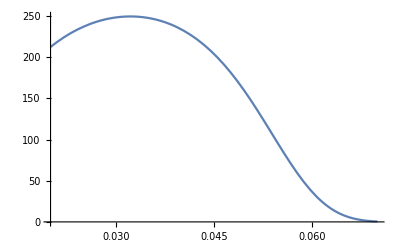
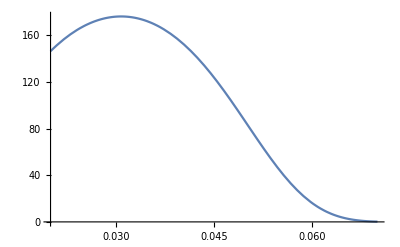
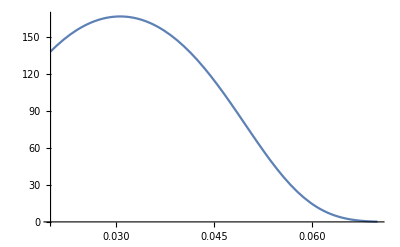
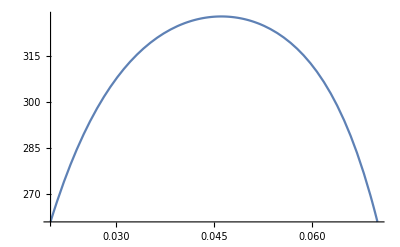
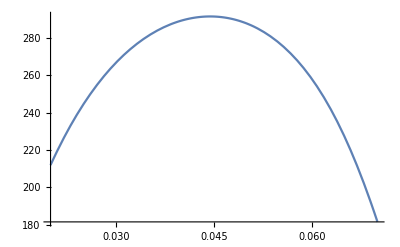
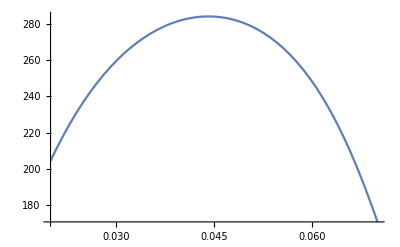
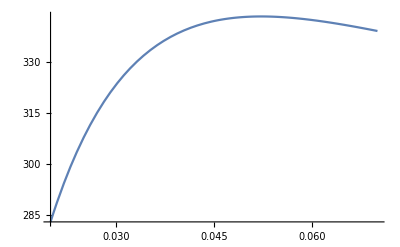
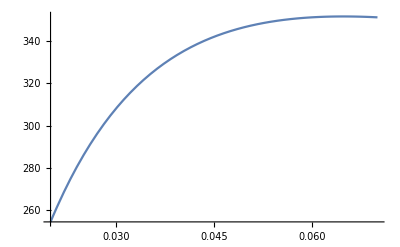

```mathematica
Plot[#,{x,0.02,0.07}]&/@(QualityTest[x,#]&/@data)
```

```mathematica
solOptimal = NMaximize[{#,x>0.02&&x<0.07},x]&/@(Re@QualityTest[x,#]&/@data)
```

{{249.658,{x→0.0322239}},{176.321,{x→0.0308008}},{166.407,{x→0.0306502}},{327.869,{x→0.0461223}},{291.52,{x→0.0444148}},{284.236,{x→0.0441627}},{343.535,{x→0.0522212}},{351.626,{x→0.0647755}},{351.62,{x→0.0660335}}}

```mathematica
Qmax=x//.({x->#⟦1⟧}&/@solOptimal);
TableForm@Qmax
```

249.658
176.321
166.407
327.869
291.52
284.236
343.535
351.626
351.62

```mathematica
diameter = x/.(#⟦2⟧&/@solOptimal);
TableForm@diameter
```

0.0322239
0.0308008
0.0306502
0.0461223
0.0444148
0.0441627
0.0522212
0.0647755
0.0660335

```mathematica
dataTemp=Table[Flatten@{diameter⟦i⟧,data⟦i⟧},{i,1,9}]//N;
TableForm@dataTemp
```

0.0322239 | 0.0762 | 0.003275
0.0308008 | 0.0762 | 0.0047625
0.0306502 | 0.0762 | 0.005
0.0461223 | 0.1016 | 0.003275
0.0444148 | 0.1016 | 0.0047625
0.0441627 | 0.1016 | 0.005
0.0522212 | 0.1524 | 0.003275
0.0647755 | 0.1524 | 0.0047625
0.0660335 | 0.1524 | 0.005

```mathematica
h=CoilHeight[#⟦1⟧,#⟦2⟧,2#⟦3⟧,Subscript[f, 0],Subscript[C, t],Subscript[C, w]]&/@dataTemp;
TableForm@h
```

0.145042
0.243533
0.259589
0.0889525
0.152842
0.163695
0.0741389
0.0911192
0.0947215

```mathematica
dataAll=Table[Flatten@{dataTemp⟦i,2⟧,dataTemp⟦i,3⟧,Qmax⟦i⟧,dataTemp⟦i,1⟧,h⟦i⟧},{i,1,9}]//N;
TableForm@dataAll
```

0.0762 | 0.003275 | 249.658 | 0.0322239 | 0.145042
0.0762 | 0.0047625 | 176.321 | 0.0308008 | 0.243533
0.0762 | 0.005 | 166.407 | 0.0306502 | 0.259589
0.1016 | 0.003275 | 327.869 | 0.0461223 | 0.0889525
0.1016 | 0.0047625 | 291.52 | 0.0444148 | 0.152842
0.1016 | 0.005 | 284.236 | 0.0441627 | 0.163695
0.1524 | 0.003275 | 343.535 | 0.0522212 | 0.0741389
0.1524 | 0.0047625 | 351.626 | 0.0647755 | 0.0911192
0.1524 | 0.005 | 351.62 | 0.0660335 | 0.0947215

```mathematica
TableForm@(Frequency[#⟦4⟧,#⟦5⟧,#⟦1⟧,#⟦2⟧*2,Subscript[C, t],Subscript[C, w]]&/@dataAll)
```

2.54726×10^7
4.02903×10^7 | 2.02093×10^7
2.56215×10^7
2.36684×10^7
3.82924×10^7 | 2.01798×10^7
2.71911×10^7
2.34824×10^7
3.80495×10^7 | 2.01748×10^7
2.73785×10^7
2.72119×10^7
3.98204×10^7 | 2.01925×10^7
2.40232×10^7
2.50299×10^7
3.87461×10^7 | 2.0235×10^7
2.57156×10^7
2.4789×10^7
3.8554×10^7 | 2.02347×10^7
2.5926×10^7
2.94334×10^7
3.95746×10^7 | 2.01481×10^7
2.26596×10^7
2.69536×10^7
3.71296×10^7 | 2.01489×10^7
2.34915×10^7
2.66715×10^7
3.69404×10^7 | 2.01552×10^7
2.36444×10^7

## Geometry factor estimation(scale)

ζ=√(4/π^2 √(μ_0/ϵ_0)Log[D/d]),
V=ζ √PQ

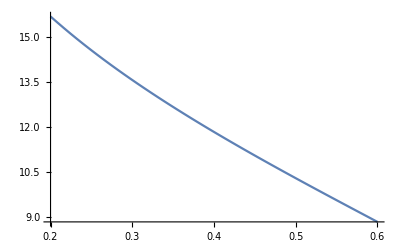

```mathematica
Plot[√(4/π^2 √(Subscript[μ, 0]/Subscript[ϵ, 0])Log[1/x]),{x,0.2,0.6}]
```